```mathematica
frl=<||>;
xi=0;
w=0.5;
```

```mathematica
frl[xi]=w;
```

```mathematica
xi
```

0.5

```mathematica
frl[xi]
```

1.

```mathematica
Table[
frl[frl[xi]]=Cos[xi];
xi=frl[xi];
, {i, 10}];
```

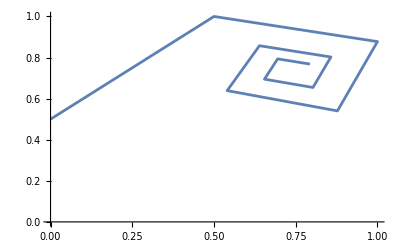

```mathematica
ListLinePlot[Transpose[{Keys[frl], Values[frl]}], PlotRange->All]
```

```mathematica
f[x_]:=1+x^2;
frlo=<||>;
Manipulate[Module[{frl=<||>,xi=xii},
frl[xi]=w;
Table[
frl[frl[xi]]=f[xi];
xi=frl[xi];
, {i, 10}];
frlo=frl;
ListLinePlot[Sort[Transpose[{Keys[frl], Values[frl]}], #1[[1]]<#2[[1]]&]]
], {w, 0, 1}, {xii, 0, 1}]
```

```mathematica
approx[x_]:=Interpolation[Transpose[{Keys@frlo, Values@frlo}], InterpolationOrder->1][x];

Manipulate[Show[Plot[approx[approx[x]], {x, 0, 2^m}, PlotStyle->Orange, PlotRange->All],
Plot[f[x], {x, 0, 2^m}]], {m, 0, 10}]
```

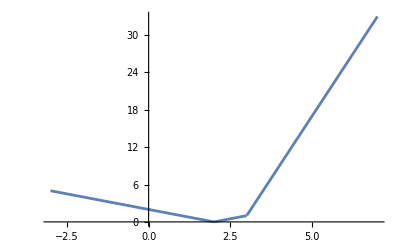

<|0.2→0.3,0.3→1.04,1.04→1.09,1.09→2.0816,2.0816→2.1881,2.1881→5.33306,5.33306→5.78778,5.78778→29.4415,29.4415→34.4984,34.4984→867.803,867.803→1191.14|>

<|0.2→0.1,0.1→1.04,1.04→1.01,1.01→2.0816,2.0816→2.0201,2.0201→5.33306,5.33306→5.0808,5.0808→29.4415,29.4415→26.8146,26.8146→867.803,867.803→720.021|>

<|0.2→0.1,0.1→1.04,1.04→1.01,1.01→2.0816,2.0816→2.0201,2.0201→5.33306,5.33306→5.0808,5.0808→29.4415,29.4415→26.8146,26.8146→867.803,867.803→720.021|>

<|0.2→0.1,0.1→1.04,1.04→1.01,1.01→2.0816,2.0816→2.0201,2.0201→5.33306,5.33306→5.0808,5.0808→29.4415,29.4415→26.8146,26.8146→867.803,867.803→720.021|>

«179 more identical outputs»

$Aborted

<|0.→1.,Missing[KeyAbsent,1.]→2.,2.→1+Missing[KeyAbsent,1.]^2,1+Missing[KeyAbsent,1.]^2→5.,5.→1+(1+Missing[KeyAbsent,1.]^2)^2,1+(1+Missing[KeyAbsent,1.]^2)^2→26.,26.→1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2,1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2→677.,677.→1+(1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2)^2,1+(1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2)^2→458330.|>

<|0.→1.,Missing[KeyAbsent,1.]→2.,2.→1+Missing[KeyAbsent,1.]^2,1+Missing[KeyAbsent,1.]^2→5.,5.→1+(1+Missing[KeyAbsent,1.]^2)^2,1+(1+Missing[KeyAbsent,1.]^2)^2→26.,26.→1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2,1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2→677.,677.→1+(1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2)^2,1+(1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2)^2→458330.|>

<|0.→1.,Missing[KeyAbsent,1.]→2.,2.→1+Missing[KeyAbsent,1.]^2,1+Missing[KeyAbsent,1.]^2→5.,5.→1+(1+Missing[KeyAbsent,1.]^2)^2,1+(1+Missing[KeyAbsent,1.]^2)^2→26.,26.→1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2,1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2→677.,677.→1+(1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2)^2,1+(1+(1+(1+Missing[KeyAbsent,1.]^2)^2)^2)^2→458330.|>

«39 more identical outputs»

$Aborted

```mathematica
LinearSpline[points_,x_]:=Module[{p, m, xs},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
Plot[LinearSpline[{{0, 2}, {3, 1}, {2, 0}, {4, 9}},x],{x, -3,7}]

f[x_]:=1+x^2;
range={0, 2, 0.1};

thing[xii_, w_]:=Module[{frl=<||>,xi=xii},
frl[xi]=w;
Table[
frl[frl[xi]]=f[xi];
xi=frl[xi];
, {i, 10}];
frl
]

thing[0.2, 0.3]

thingFunc[xii_, w_, x_]:=If[#===<||>, 2^16, LinearSpline[Transpose[{Keys[#], Values[#]}],x]]&@Echo@thing[xii, w]

Plot[thingFunc[0.2,0.1,x],{x,range[[1]], range[[2]]}]

errorFunc[xii_, w_]:=Sum[(thingFunc[xii, w, thingFunc[xii, w, x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}]
errorFunc[0., 0.]
```

```mathematica
indices={{0.,0.},{0.,0.5},{0.,0.99},{0.5,0.},{0.5,0.5},{0.5,0.99},{0.99,0.},{0.99,0.5},{0.99,0.99}};
loss=errorFunc;
d=0.001;
varsAndBounds={{xii, 0, 1, 0.5}, {w, 0, 1, 0.5}};

id=First[indices]

loss@@id
loss@@(id+d*IdentityMatrix[Length[varsAndBounds]])
(loss@@(#+d*IdentityMatrix[Length[varsAndBounds]])-loss@@#)/d&[id]
(loss@@(#+d*IdentityMatrix[Length[varsAndBounds]])-loss@@#)/d&/@indices
```

{0.,0.}

$Aborted

$Aborted

```mathematica
.
```

```mathematica
plots={};
gridDescentPlotMinimize[loss_, varsAndBounds_, iters_:20, tempInput_:None, d_:0.0001]:=
Module[
{temp=If[tempInput===None, Mean[varsAndBounds[[All, 4]]]/10,tempInput],
indices=Flatten[Table@@Prepend[varsAndBounds, varsAndBounds[[All, 1]]], Length[varsAndBounds]-1],
gradients, progress=PrintTemporary["0% Complete"],
plotFunc=Switch[Length[varsAndBounds],
1,ListPlot[#, PlotRange->varsAndBounds[[1, 2;;3]]]&,
2,ListPlot[#, PlotRange->varsAndBounds[[All, 2;;3]]]&,
3,ListPointPlot3D[#, PlotRange->varsAndBounds[[All, 2;;3]]]&,
_,"No Plot"&]},
indices=Table[Clip[#[[i]], varsAndBounds[[i, 2;;3]]- d],{i, Length[varsAndBounds]}]&/@indices;
plots={plotFunc[indices]};
Table[
gradients=(loss@@(#+d*IdentityMatrix[Length[varsAndBounds]])-loss@@#)/d&/@indices;
gradients=Function[{v}, Clip[#, {-10temp, 10temp}]&/@v]/@gradients;
indices=indices-temp*gradients;
indices=Table[Clip[#[[i]], varsAndBounds[[i, 2;;3]]- d],{i, Length[varsAndBounds]}]&/@indices;
AppendTo[plots, plotFunc@indices];
NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*iter/iters]]<>"% Complete"];
, {iter, iters}];
Labeled[ListAnimate[plots],indices[[Position[loss@@@indices, Min[loss@@@indices]][[1, 1]]]]]
]
```

```mathematica
gridDescentPlotMinimize[errorFunc, {{xii, 0, 1, 0.1}, {w, 0, 1, 0.1}}]
```

```mathematica
$Aborteds
```

```mathematica
plots
```

```mathematica
ContourPlot[Log[errorFunc[xii, w]], {xii, 0, 1}, {w, 0, 1}, AxesLabel->{"xii", "w", "e"}]
```

$Aborted

-Graphics3D-

```mathematica
frmi=thing@@Values[Last[mi]]
approx[x_]:=Interpolation[Transpose[{Keys@frmi, Values@frmi}], InterpolationOrder->1][x];
```

<|0.389882→-0.638988,-0.638988→1.15201,1.15201→1.40831,1.40831→2.32712,2.32712→2.98333,2.98333→6.4155,6.4155→9.90024,9.90024→42.1586,42.1586→99.0147,99.0147→1778.35,1778.35→9804.9|>

```mathematica
Manipulate[Show[Plot[approx[x], {x, 0, 2^m}, PlotStyle->Orange, PlotRange->All],
Plot[f[x], {x, 0, 2^m}]], {m, 0, 4}]
```